# Ecuaciones diferenciales: Método de Euler

## Representación gráfica para el punto x_0= 1, y(x_0) = 1

```mathematica
f[x_,y_]=x^2-y^2;
```

```mathematica
xn = 1;
yn = 1;
h = 0.3;
results = {{xn,yn}};

Do[
xnp = xn + h;
ynp= yn + h f[xn,yn];
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,10
]
```

```mathematica
results
```

{{1,1},{1.3,1.},{1.6,1.207},{1.9,1.53795},{2.2,1.91136},{2.5,2.26737},{2.8,2.60008},{3.1,2.92396},{3.4,3.2421},{3.7,3.55674},{4.,3.86863}}

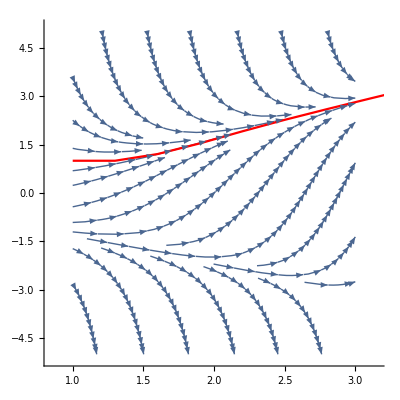

```mathematica
Show[
StreamPlot[{1,f[x,y]},{x,1,3},{y,-5,5},Frame->False,Axes->True],
ListLinePlot[results,PlotStyle->{Red}]
]
```

## Representación gráfica interactiva

```mathematica
MetodoEuler[{x0_,y0_},h_,n_]:=Block[{xn,yn,results,xnp,ynp},
xn = x0;
yn = y0;
results = {{xn,yn}};

Do[
xnp = xn + h;
ynp= yn + h f[xn,yn];
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,n
];

results
];
```

```mathematica
Manipulate[
Show[
StreamPlot[
{1,f[x,y]},{x,1,3},{y,-5,5},
PlotRange->{{1,3},{-5,5}},
Frame->True,
ImageSize->450,
BaseStyle->FontSize->13,
FrameLabel->{Style["x",15], Style["y",15]},
PlotTheme->"Monochrome",
GridLines->Automatic
],
ListLinePlot[MetodoEuler[p,0.1,10],PlotStyle->{Red}]
],
{{p,{1,1}},Locator}
]
```